# RQA Exploration

Alison Ord

Flip Phillips

## To do notes

6 July 2019
* Find out why some of the stuff working yesterday afternoon wasn’t working come evening!
* Try to obtain numbers for the RQA’s instead of the timeseries boxes - you seem to have got the right number of boxes
* Plot the numbers against the value of the timeseries - and modify the existing plots so that the x axis represents the absolute position within the timeseries, not just the position within the epoch
* Work out how to interrogate a particular RQA while moving through the data - 12 little recurrence plots look very pretty - but how about when you interrogate 120,000 points, 260,000 points, 1 trillion points?
* Consider Meredith’s code for a moving window collecting data during loading, and throwing away the data until their chosen event occurs, and then retaining the immediately prior windows, and then windows during and after the event.

## Load FP’s RQA package

```mathematica
gitHubDir=ResourceFunction["NotebookRelativePath"][{"..","..","..","RQA","RQA"}]
```

C:\Users\Alison\Documents\GitHub\WSS2019-ao\Final Project\Drafts\..\..\..\RQA\RQA

```mathematica
Get[FileNameJoin[{gitHubDir,"RQA.wl"}]]
```

```mathematica
?RQA`*
```

```mathematica
<<RQA`
```

Get::noopen: Cannot open RQA`.

$Failed

The package is built on the equations expressed in Webber and Marwan (2015).

## Find and load the data

```mathematica
(* data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","rock4z.dat"}]]]; *)
```

```mathematica
data=Flatten[Import[ResourceFunction["NotebookRelativePath"][{"..","Data","r30datab.dat"}]]] ;
```

data=Flatten[Import["C:\Users\Alison\Documents\Personal\Wolfram Summer School\Projects\Rule30Results\r30datab.dat"]]

We start by using the data from the same folded rock, or to Rule30, to which we applied the nonlinear tools of spatial attractor, wavelet transform (2D and 3D), Hurst exponents, singularity spectrum (not yet in mtca), and so on.

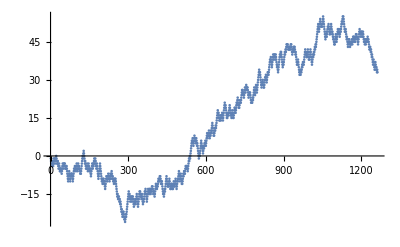

```mathematica
ListPlot[data]
```

We create a time series in the form required by mtca.

```mathematica
ds=RQAMakeTimeSeries[data,1,1]
```

TimeSeries[…]

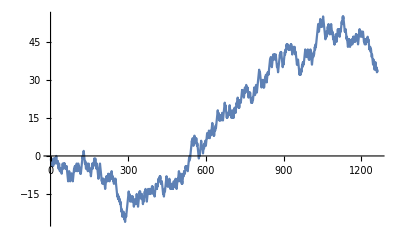

```mathematica
ListLinePlot[ds]
```

Trial some predictions based on existing mtca functions

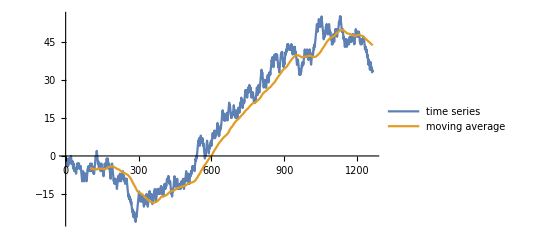

```mathematica
avg=MovingAverage[ds,100];
ListLinePlot[{ds,avg},PlotLegends->{"time series","moving average"}]
```

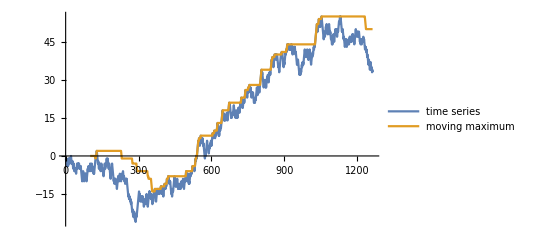

```mathematica
max=MovingMap[Max,ds,100];
ListLinePlot[{ds,max},PlotLegends->{"time series","moving maximum"}]
```

```mathematica
dsm=TimeSeriesModelFit[ds]
```

TimeSeriesModel[…]

Use TimeSeriesForecastpaclet:ref/TimeSeriesForecast to forecast the next 1000 values in the time series:

```mathematica
dsf=TimeSeriesForecast[dsm,{1000}];
```

Plot the time series along with the forecast:

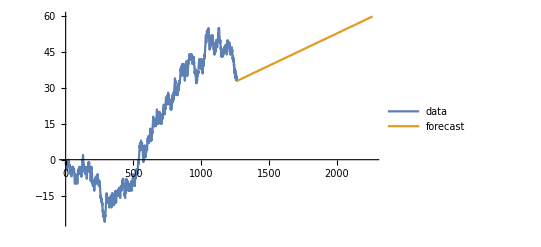

```mathematica
ListLinePlot[{ds,dsf},PlotLegends->{"data","forecast"}]
```

```mathematica
eproc=TimeSeriesModelFit[ds,{"SARIMA",12}]["Process"]
```

SARIMAProcess[-0.00155134,{0.0818105},1,{},{12,{-0.0655016},1,{-0.863972}},1.10781]

```mathematica
forecast=TimeSeriesForecast[eproc,ds,{1000}];
```

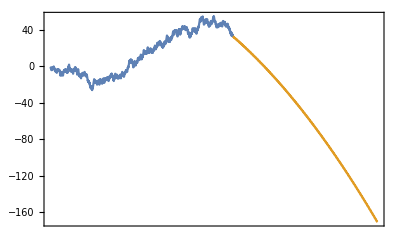

```mathematica
DateListPlot[{ds,forecast},Joined->True]
```

## Estimate the lag and embedding dimensions for the data

The lag is first estimated-

```mathematica
lag=RQAEstimateLag[ds]
```

409.373

However, a lag of 10 was used in previously published work (Ord&Hobbs, 2018; Ord et al., 2018) so that is what we will use here.

```mathematica
lag=10
```

10

The embedding dimension of the system is then estimated. The result below suggests a dimension of 3.

```mathematica
RQAEstimateDimensionality[ds,lag]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::pkspec1: The expression {First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»} cannot be used as a part specification.

MapThread::mptd: Object {-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,«13»,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

10 Mean[MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-4.,-3.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-7.,-8.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-5.,-6.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-5.,-6.,-5.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,-1.,0.,1.,2.,1.,0.,-1.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-11.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-10.,-11.,-12.,-13.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-18.,-19.,-18.,-19.,-20.,-21.,-22.,-21.,-22.,-23.,-24.,-23.,-22.,-23.,-22.,-23.,-24.,-25.,-24.,-25.,-26.,-25.,-24.,-23.,-24.,-23.,-22.,-21.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-19.,-18.,-17.,-18.,-19.,-18.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-18.,-17.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-13.,-14.,-15.,-16.,-17.,-18.,-17.,-16.,-15.,-14.,-13.,-14.,-15.,-14.,-15.,-14.,-13.,-14.,-13.,-14.,-15.,-14.,-13.,-14.,-13.,-12.,-13.,-12.,-13.,-14.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-11.,-12.,-13.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-10.,-11.,-12.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-10.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-9.,-8.,-7.,-8.,-7.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-2.,-1.,-2.,-1.,0.,-1.,0.,1.,2.,3.,4.,5.,6.,5.,6.,7.,6.,5.,4.,5.,6.,7.,8.,7.,6.,7.,6.,5.,6.,7.,6.,5.,4.,5.,4.,3.,2.,1.,0.,-1.,0.,1.,0.,1.,2.,3.,4.,5.,6.,5.,4.,3.,4.,3.,2.,1.,2.,3.,4.,3.,4.,5.,4.,5.,6.,5.,4.,5.,6.,7.,8.,9.,8.,7.,8.,9.,8.,9.,10.,9.,8.,7.,8.,9.,8.,9.,10.,9.,10.,11.,12.,13.,12.,11.,10.,9.,8.,9.,8.,9.,10.,11.,10.,11.,12.,11.,12.,13.,14.,15.,16.,17.,18.,17.,16.,17.,16.,15.,14.,15.,14.,15.,16.,15.,14.,15.,16.,15.,16.,17.,16.,15.,14.,15.,16.,17.,18.,19.,20.,21.,20.,19.,20.,19.,18.,17.,16.,15.,16.,15.,16.,17.,16.,17.,16.,17.,18.,19.,20.,19.,18.,17.,16.,17.,16.,15.,16.,17.,18.,17.,16.,15.,16.,15.,16.,17.,18.,19.,18.,19.,18.,17.,18.,19.,20.,21.,20.,21.,22.,23.,22.,21.,20.,19.,20.,19.,20.,21.,22.,21.,22.,21.,22.,23.,24.,25.,26.,25.,26.,25.,24.,25.,24.,23.,24.,25.,26.,27.,26.,25.,26.,27.,28.,27.,26.,27.,26.,27.,26.,25.,24.,23.,24.,25.,24.,25.,24.,25.,24.,23.,22.,21.,22.,21.,22.,21.,22.,23.,22.,23.,24.,25.,26.,27.,26.,25.,24.,25.,26.,27.,28.,27.,26.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,33.,32.,33.,32.,31.,30.,29.,28.,27.,28.,29.,28.,29.,30.,29.,28.,27.,28.,27.,28.,29.,30.,31.,30.,31.,32.,31.,30.,29.,30.,31.,32.,33.,32.,33.,32.,33.,34.,35.,36.,37.,38.,37.,38.,39.,38.,37.,36.,35.,36.,37.,38.,39.,40.,39.,38.,39.,40.,39.,40.,39.,38.,39.,40.,39.,38.,37.,36.,35.,36.,35.,34.,33.,34.,35.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,40.,39.,38.,37.,36.,35.,36.,37.,36.,37.,38.,39.,40.,41.,40.,41.,42.,41.,42.,43.,44.,43.,44.,43.,44.,43.,42.,43.,42.,43.,42.,43.,42.,43.,42.,43.,44.,43.,44.,43.,42.,41.,40.,41.,42.,41.,42.,43.,42.,43.,42.,43.,42.,41.,40.,41.,40.,39.,38.,37.,36.,37.,36.,37.,38.,37.,36.,35.,34.,33.,32.,33.,34.,33.,32.,33.,34.,33.,34.,35.,36.,35.,36.,37.,36.,37.,36.,37.,38.,39.,40.,41.,42.,41.,40.,41.,40.,39.,40.,39.,40.,41.,42.,41.,40.,39.,38.,39.,38.,39.,40.,41.,42.,41.,40.,39.,38.,37.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,42.,43.,42.,43.,44.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,51.,50.,49.,50.,51.,52.,53.,54.,53.,52.,51.,52.,51.,52.,51.,52.,53.,54.,55.,54.,53.,52.,51.,50.,49.,48.,47.,46.,47.,48.,49.,48.,47.,48.,49.,50.,51.,50.,51.,52.,51.,50.,49.,48.,49.,48.,49.,50.,51.,52.,51.,50.,49.,48.,49.,48.,47.,46.,47.,46.,45.,44.,45.,44.,45.,46.,47.,48.,47.,46.,45.,46.,47.,48.,49.,50.,49.,48.,49.,50.,49.,48.,47.,48.,49.,50.,49.,50.,51.,52.,53.,52.,53.,54.,55.,54.,55.,54.,53.,52.,51.,50.,49.,50.,49.,50.,49.,48.,47.,46.,47.,46.,45.,44.,43.,44.,45.,46.,45.,46.,45.,44.,43.,44.,45.,44.,45.,44.,45.,46.,45.,44.,45.,46.,47.,46.,47.,46.,45.,46.,47.,46.,45.,46.,47.,48.,47.,48.,47.,46.,47.,46.,45.,44.,45.,46.,47.,48.,49.,50.,49.,48.,49.,48.,47.,48.,49.,48.,49.,48.,47.,48.,49.,48.,47.,46.,45.,46.,45.,44.,45.,46.,45.,44.,45.,46.,45.,46.,45.,46.,47.,46.,45.,46.,45.,44.,43.,42.,43.,42.,43.,42.,41.,42.,41.,40.,39.,40.,39.,38.,37.,36.,37.,38.,37.,36.,35.,34.,35.,36.,37.,36.,35.,34.,35.,34.,33.,34.,33.},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-4.,-3.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-7.,-8.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-5.,-6.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-5.,-6.,-5.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,-1.,0.,1.,2.,1.,0.,-1.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-11.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-10.,-11.,-12.,-13.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-18.,-19.,-18.,-19.,-20.,-21.,-22.,-21.,-22.,-23.,-24.,-23.,-22.,-23.,-22.,-23.,-24.,-25.,-24.,-25.,-26.,-25.,-24.,-23.,-24.,-23.,-22.,-21.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-19.,-18.,-17.,-18.,-19.,-18.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-18.,-17.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-13.,-14.,-15.,-16.,-17.,-18.,-17.,-16.,-15.,-14.,-13.,-14.,-15.,-14.,-15.,-14.,-13.,-14.,-13.,-14.,-15.,-14.,-13.,-14.,-13.,-12.,-13.,-12.,-13.,-14.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-11.,-12.,-13.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-10.,-11.,-12.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-10.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-9.,-8.,-7.,-8.,-7.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-2.,-1.,-2.,-1.,0.,-1.,0.,1.,2.,3.,4.,5.,6.,5.,6.,7.,6.,5.,4.,5.,6.,7.,8.,7.,6.,7.,6.,5.,6.,7.,6.,5.,4.,5.,4.,3.,2.,1.,0.,-1.,0.,1.,0.,1.,2.,3.,4.,5.,6.,5.,4.,3.,4.,3.,2.,1.,2.,3.,4.,3.,4.,5.,4.,5.,6.,5.,4.,5.,6.,7.,8.,9.,8.,7.,8.,9.,8.,9.,10.,9.,8.,7.,8.,9.,8.,9.,10.,9.,10.,11.,12.,13.,12.,11.,10.,9.,8.,9.,8.,9.,10.,11.,10.,11.,12.,11.,12.,13.,14.,15.,16.,17.,18.,17.,16.,17.,16.,15.,14.,15.,14.,15.,16.,15.,14.,15.,16.,15.,16.,17.,16.,15.,14.,15.,16.,17.,18.,19.,20.,21.,20.,19.,20.,19.,18.,17.,16.,15.,16.,15.,16.,17.,16.,17.,16.,17.,18.,19.,20.,19.,18.,17.,16.,17.,16.,15.,16.,17.,18.,17.,16.,15.,16.,15.,16.,17.,18.,19.,18.,19.,18.,17.,18.,19.,20.,21.,20.,21.,22.,23.,22.,21.,20.,19.,20.,19.,20.,21.,22.,21.,22.,21.,22.,23.,24.,25.,26.,25.,26.,25.,24.,25.,24.,23.,24.,25.,26.,27.,26.,25.,26.,27.,28.,27.,26.,27.,26.,27.,26.,25.,24.,23.,24.,25.,24.,25.,24.,25.,24.,23.,22.,21.,22.,21.,22.,21.,22.,23.,22.,23.,24.,25.,26.,27.,26.,25.,24.,25.,26.,27.,28.,27.,26.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,33.,32.,33.,32.,31.,30.,29.,28.,27.,28.,29.,28.,29.,30.,29.,28.,27.,28.,27.,28.,29.,30.,31.,30.,31.,32.,31.,30.,29.,30.,31.,32.,33.,32.,33.,32.,33.,34.,35.,36.,37.,38.,37.,38.,39.,38.,37.,36.,35.,36.,37.,38.,39.,40.,39.,38.,39.,40.,39.,40.,39.,38.,39.,40.,39.,38.,37.,36.,35.,36.,35.,34.,33.,34.,35.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,40.,39.,38.,37.,36.,35.,36.,37.,36.,37.,38.,39.,40.,41.,40.,41.,42.,41.,42.,43.,44.,43.,44.,43.,44.,43.,42.,43.,42.,43.,42.,43.,42.,43.,42.,43.,44.,43.,44.,43.,42.,41.,40.,41.,42.,41.,42.,43.,42.,43.,42.,43.,42.,41.,40.,41.,40.,39.,38.,37.,36.,37.,36.,37.,38.,37.,36.,35.,34.,33.,32.,33.,34.,33.,32.,33.,34.,33.,34.,35.,36.,35.,36.,37.,36.,37.,36.,37.,38.,39.,40.,41.,42.,41.,40.,41.,40.,39.,40.,39.,40.,41.,42.,41.,40.,39.,38.,39.,38.,39.,40.,41.,42.,41.,40.,39.,38.,37.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,42.,43.,42.,43.,44.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,51.,50.,49.,50.,51.,52.,53.,54.,53.,52.,51.,52.,51.,52.,51.,52.,53.,54.,55.,54.,53.,52.,51.,50.,49.,48.,47.,46.,47.,48.,49.,48.,47.,48.,49.,50.,51.,50.,51.,52.,51.,50.,49.,48.,49.,48.,49.,50.,51.,52.,51.,50.,49.,48.,49.,48.,47.,46.,47.,46.,45.,44.,45.,44.,45.,46.,47.,48.,47.,46.,45.,46.,47.,48.,49.,50.,49.,48.,49.,50.,49.,48.,47.,48.,49.,50.,49.,50.,51.,52.,53.,52.,53.,54.,55.,54.,55.,54.,53.,52.,51.,50.,49.,50.,49.,50.,49.,48.,47.,46.,47.,46.,45.,44.,43.,44.,45.,46.,45.,46.,45.,44.,43.,44.,45.,44.,45.,44.,45.,46.,45.,44.,45.,46.,47.,46.,47.,46.,45.,46.,47.,46.,45.,46.,47.,48.,47.,48.,47.,46.,47.,46.,45.,44.,45.,46.,47.,48.,49.,50.,49.,48.,49.,48.,47.,48.,49.,48.,49.,48.,47.,48.,49.,48.,47.,46.,45.,46.,45.,44.,45.,46.,45.,44.,45.,46.,45.,46.,45.,46.,47.,46.,45.,46.,45.,44.,43.,42.,43.,42.,43.,42.,41.,42.,41.,40.,39.,40.,39.,38.,37.,36.,37.,38.,37.,36.,35.,34.,35.,36.,37.,36.,35.,34.,35.,34.,33.,34.,33.}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,5,6,5,6,5,6,31,6,31,6,31,6,31,36,43,First[{}],First[{}],First[{}],67,66,43,36,43,66,67,68,67,66,43,66,43,66,43,66,67,68,67,66,43,36,31,36,31,6,31,6,31,36,31,6,5,6,31,36,31,6,5,6,31,6,31,36,31,36,43,36,43,36,31,6,5,2,1,22,1,22,First[{}],First[{}],127,22,1,2,5,2,5,6,31,6,31,6,5,6,31,36,31,6,5,6,31,36,31,36,31,36,43,66,43,36,31,6,5,6,31,6,5,6,5,2,1,2,5,2,1,2,5,6,31,6,5,6,31,36,43,66,67,66,43,36,31,6,5,6,31,36,43,66,67,68,67,68,First[{}],68,67,68,67,68,201,68,201,First[{}],First[{}],210,201,68,67,66,67,66,67,68,67,66,43,66,67,66,67,68,67,66,43,66,67,66,43,36,43,66,67,66,67,68,67,68,201,68,67,68,67,68,67,68,201,210,211,First[{}],First[{}],First[{}],257,258,First[{}],258,261,258,261,First[{}],261,266,First[{}],266,269,269,272,First[{}],273,274,First[{}],First[{}],277,274,277,274,277,278,278,278,285,285,285,278,277,278,277,274,273,272,269,266,261,258,257,256,257,258,257,258,261,266,261,258,261,258,261,266,261,258,261,258,261,266,269,272,269,266,269,266,261,266,269,266,261,258,257,258,261,266,269,272,269,266,261,258,257,256,257,256,257,258,257,258,261,258,257,258,261,266,269,266,261,266,261,258,257,256,257,256,211,256,257,258,261,266,261,258,257,256,211,256,257,256,257,256,211,256,211,256,257,256,211,256,211,210,211,210,211,256,257,256,257,256,257,258,257,256,211,210,201,210,211,210,211,210,201,210,201,68,67,68,67,68,67,66,67,66,67,68,201,68,201,68,201,210,211,256,257,256,257,258,257,256,211,256,211,210,201,68,67,66,67,68,201,210,201,210,201,210,201,68,67,68,201,210,211,210,211,210,201,210,201,210,211,210,211,210,201,68,201,210,201,210,201,68,67,68,201,210,211,210,201,68,67,68,67,66,43,36,43,66,67,68,67,66,43,66,67,68,201,68,201,68,67,66,43,66,43,36,43,36,43,36,31,6,31,6,31,6,31,6,31,36,31,6,5,2,1,2,1,22,1,22,127,128,First[{}],First[{}],First[{}],First[{}],545,546,First[{}],546,545,544,545,546,549,First[{}],549,546,549,546,545,546,549,546,545,544,545,544,543,128,127,22,1,22,127,22,127,128,543,544,545,546,545,544,543,544,543,128,127,128,543,544,543,544,545,544,545,546,545,544,545,546,549,556,First[{}],556,549,556,605,556,605,First[{}],605,556,549,556,605,556,605,612,605,612,First[{}],623,624,624,623,612,605,556,605,556,605,612,623,612,623,624,623,624,625,First[{}],First[{}],First[{}],First[{}],First[{}],645,644,645,644,643,642,643,642,643,644,643,642,643,644,643,644,645,644,643,642,643,644,645,646,First[{}],First[{}],First[{}],672,671,672,671,646,645,644,643,644,643,644,645,644,645,644,645,646,671,672,671,646,645,644,645,644,643,644,645,646,645,644,643,644,643,644,645,646,671,646,671,646,645,646,671,672,673,672,673,First[{}],First[{}],722,673,672,671,672,671,672,673,722,673,722,673,722,723,First[{}],First[{}],First[{}],739,740,739,738,739,738,723,738,739,740,First[{}],740,739,740,751,First[{}],751,740,751,740,751,740,739,738,723,738,739,738,739,738,739,738,723,722,673,722,673,722,673,722,723,722,723,738,739,740,751,740,739,738,739,740,751,756,751,740,739,740,751,756,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],805,804,805,804,803,802,801,756,751,756,801,756,801,802,801,756,751,756,751,756,801,802,803,802,803,804,803,802,801,802,803,804,805,804,805,804,805,806,First[{}],First[{}],First[{}],First[{}],847,848,First[{}],848,847,846,845,846,847,848,851,First[{}],851,848,851,860,851,860,851,848,851,860,851,848,847,846,845,846,845,806,805,806,845,846,847,848,851,860,851,860,First[{}],860,889,860,851,848,847,846,845,846,847,846,847,848,851,860,889,860,889,First[{}],889,908,First[{}],First[{}],911,912,911,912,911,908,911,908,911,908,911,908,911,908,911,912,911,912,911,908,889,860,889,908,889,908,911,908,911,908,911,908,889,860,889,860,851,848,847,846,847,846,847,848,847,846,845,806,805,804,805,806,805,804,805,806,805,806,845,846,845,846,847,846,847,846,847,848,851,860,889,908,889,860,889,860,851,860,851,860,889,908,889,860,851,848,851,848,851,860,889,908,889,860,851,848,847,846,847,848,851,860,851,860,889,860,889,908,911,908,911,912,911,912,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],1033,1032,1031,1032,1033,1034,First[{}],First[{}],1041,1034,1033,1034,1033,1034,1033,1034,1041,1042,1042,1042,1041,1034,1033,1032,1031,1030,1029,1028,1029,1030,1031,1030,1029,1030,1031,1032,1033,1032,1033,1034,1033,1032,1031,1030,1031,1030,1031,1032,1033,1034,1033,1032,1031,1030,1031,1030,1029,1028,1029,1028,1027,912,1027,912,1027,1028,1029,1030,1029,1028,1027,1028,1029,1030,1031,1032,1031,1030,1031,1032,1031,1030,1029,1030,1031,1032,1031,1032,1033,1034,1041,1034,1041,1042,1053,1042,1053,1042,1041,1034,1033,1032,1031,1032,1031,1032,1031,1030,1029,1028,1029,1028,1027,912,911,912,1027,1028,1027,1028,1027,912,911,912,1027,912,1027,912,1027,1028,1027,912,1027,1028,1029,1028,1029,1028,1027,1028,1029,1028,1027,1028,1029,1030,1029,1030,1029,1028,1029,1028,1027,912,1027,1028,1029,1030,1031,1032,1031,1030,1031,1030,1029,1030,1031,1030,1031,1030,1029,1030,1031,1030,1029,1028,1027,1028,1027,912,1027,1028,1027,912,1027,1028,1027,1028,1027,1028,1029,1028,1027,1028,1027,912,911,908,911,908,911,908,889,908,889,860,851,860,851,848,847,846,847,848,847,846,845,806,845,846,847,846,845,806,845,806,805,806,805}⟧}]]

Part::pkspec1: The expression {First[{}],First[{}],2,2,2,First[{}],2,2,5,6,5,3,3,2,1,2,7,2,1,First[{}],20,1,1,20,First[{}],21,25,26,25,First[{}],First[{}],30,26,30,31,First[{}],First[{}],36,31,36,37,36,36,36,37,First[{}],25,46,31,46,«1203»} cannot be used as a part specification.

MapThread::mptd: Object … at position {2, 2} in … has only 0 of required 1 dimensions.

MapThread::mptd: Object {-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,«13»,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

{Null,{{{2,0.,2,1,2,Mean[MapThread[SquaredEuclideanDistance,{{{-1.,-3.},{-2.,-2.},{-1.,-1.},{-2.,-2.},{-3.,-1.},{-4.,-2.},{-3.,-3.},{-2.,-2.},{-3.,-1.},{-4.,-2.},{-3.,-1.},{-2.,0.},{-1.,-1.},{-2.,-2.},{-1.,-3.},{-2.,-2.},1221,{42.,38.},{41.,37.},{40.,36.},{39.,35.},{40.,34.},{39.,35.},{38.,36.},{37.,37.},{36.,36.},{37.,35.},{38.,34.},{37.,35.},{36.,34.},{35.,33.},{34.,34.},{35.,33.}},1}]]}}}}
 |  |  |  |

```mathematica
embedding=RQAEmbed[ds,3,lag]
```

TimeSeries[…]

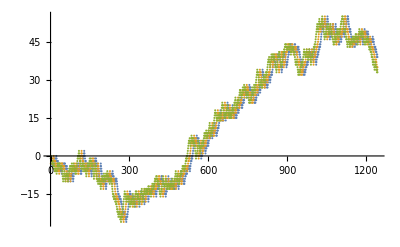

```mathematica
ListPlot[embedding]
```

## Plot the 3D spatial attractor

embedding is now a list of 3 columns of data, off set by the lag of 10, and we plot these in three dimensions, with the axes representing t, t+10, t+20

```mathematica
ParametricPlot3D[embedding[t],{t,1,650}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->{Orange,Specularity[White,10]},ViewPoint->{Left,Top}]
```

-Graphics3D-

```mathematica
ParametricPlot3D[embedding[t],{t,1,1222},PlotStyle->Directive[Green,Opacity[0.8],Specularity[White,20]],ViewPoint->{Left,Bottom}]
```

-Graphics3D-

## Interrogate the neighbours

These give you information on the neighbours, nearestneighbours and neighbours, but what is it you really need to know? Number of nearest neighbours? & don’t you normally (in VRA) search for these earlier while determining the dimensionality?

```mathematica
rn=RQANeighbors[embedding];
```

```mathematica
rnn=RQANearestNeighbors[embedding];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

```mathematica
rnd=RQANeighborDistances[embedding];
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::pkspec1: The expression {2,1,2,1,4,5,4,4,5,5,10,5,4,5,First[{}],11,10,16,15,15,20,15,16,20,20,21,26,26,25,First[{}],30,30,26,30,31,First[{}],10,36,First[{}],36,37,36,36,37,44,45,46,47,46,46,«1193»} cannot be used as a part specification.

MapThread::mptd: Object {{-1.,-3.,-1.},{-2.,-2.,0.},{-1.,-1.,-1.},{-2.,-2.,-2.},{-3.,-1.,-3.},{-4.,-2.,-2.},{-3.,-3.,-3.},{-2.,-2.,-2.},{-3.,-1.,-3.},{-4.,-2.,-4.},{-3.,-1.,-5.},{-2.,0.,-4.},{-1.,-1.,-3.},{-2.,-2.,-4.},{-1.,-3.,-5.},«21»,{-5.,-3.,-5.},{-6.,-4.,-4.},{-5.,-5.,-5.},{-6.,-4.,-4.},{-5.,-3.,-5.},{-6.,-4.,-4.},{-7.,-3.,-5.},{-6.,-4.,-6.},{-5.,-3.,-7.},{-4.,-4.,-8.},{-3.,-5.,-9.},{-4.,-4.,-10.},{-5.,-5.,-9.},{-4.,-4.,-8.},«1193»}⟦«1»⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{{-1.,-3.,-1.},{-2.,-2.,0.},{-1.,-1.,-1.},{-2.,-2.,-2.},{-3.,-1.,-3.},{-4.,-2.,-2.},{-3.,-3.,-3.},{-2.,-2.,-2.},{-3.,-1.,-3.},{-4.,-2.,-4.},{-3.,-1.,-5.},{-2.,0.,-4.},{-1.,-1.,-3.},{-2.,-2.,-4.},«24»,{-5.,-5.,-5.},{-6.,-4.,-4.},{-5.,-3.,-5.},{-6.,-4.,-4.},{-7.,-3.,-5.},{-6.,-4.,-6.},{-5.,-3.,-7.},{-4.,-4.,-8.},{-3.,-5.,-9.},{-4.,-4.,-10.},{-5.,-5.,-9.},{-4.,-4.,-8.},«1193»},{«1»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

## Calculate the distance map and the recurrence map

Webber (2012) numerical examples provide explicit step-by-step details on how input vectors (data) are delayed, embedded, normed, and rescaled
to define elements (distances) in the distance matrix (DM). Also described is how the recurrence matrix (RM) is derived from the DM by selecting only those recurrent points with distances falling within a selected RADIUS. Understanding of these simple examples should remove the mathematical mystery behind the basis of recurrence quantification analysis which simply finds patterns among recurrent points according to objective rules.
README_2012.PDF

Webber Chap 2.pdf the radius parameter implements a cut-off limit (Heavyside function) that transforms the distance matrix
(DM) into the recurrence matrix (RM). That is, all (i, j) elements in DM with distances at or below the RADIUS cutoff are included in the
recurrence matrix (element value = 1), but all other elements are excluded from RM (element value = 0). Note carefully that the RM
derives from the DM, but the two matrices are not identical.

FlipPhillips (pers.comm. 2019) Let us now look at the distance map. 1) recurrence maps are computed from distance maps.
2) distance maps are constant for any given embedding
3) recurrence maps are distance maps thresholded on a given distance
3a) If you don’t supply a threshold radius in the recurrence map command one will be computed for you (mean of all distances in the map)
4) ‘recurrence maps’ as created by your/my program a) use a strange distance measure that seems to be 100x the ‘real’ distance in Euclidean space and b) are a _combination_ of the distance map thresholded by the recurrence map.

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the distance map

```mathematica
dm=RQADistanceMap[embedding];
MatrixPlot[dm,DataReversed->{True,False},PlotRange->All,ColorFunction->Hue]
```

-Graphics-

The minimum and maximum are  determined to be 0 and 0.224875 - for rock4z
0 and 17251 for Rule30!

```mathematica
MinMax[dm]
```

{0.,17251.}

find its dimensions

```mathematica
Dimensions[dm]
```

{1243,1243}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[dm]]
```

1243

Using these values for the lag of 10 and for the embedding dimension of 3, we can now calculate the recurrence map

```mathematica
Mean[Flatten[dm]]
```

3462.13

So the automatic radius for Rule30 is 3462.13

```mathematica
rm=RQARecurrenceMap[embedding];
```

find its dimensions

```mathematica
Dimensions[rm]
```

{1243,1243}

and the first number in the expression, that is, in the list of dimensions

```mathematica
First[Dimensions[rm]]
```

1243

The recurrence map may be plotted

```mathematica
MatrixPlot[rm,DataReversed->{True,False},PlotRange->All,ColorFunction->(RGBColor[1-#,#,1/2]&)]
```

-Graphics-

The minimum and maximum of the recurrence are determined to be 0 and 1 respectively.

```mathematica
MinMax[rm]
```

{0,1}

## Calculate the RQA measures; compare with those using Webber’s RQA software

```mathematica
N[RQARecurrence[rm]]
```

0.6179

This compares with %REC=40.2 which is the result from Webber’s RQA for embedding dimension of 3 and a lag of 10

```mathematica
N[RQADeterminism[rm]]
```

0.998524

%DET=99.9 Result from RQA

```mathematica
N[RQALaminarity[rm,3]]
```

0.997767

%LAM=100 Result from RQA

```mathematica
N[RQATrappingTime[rm]]
```

187.69

TT=121.8 Result from RQA

```mathematica
N[RQATrend[rm]]
```

General::munfl: Exp[-3623.59] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-2033.75] is too small to represent as a normalized machine number; precision may be lost.

-40.2534

Trend -56.4 Result from RQA

```mathematica
N[RQAEntropy[rm]]
```

6.66644

Entropy 7.6 Result from RQA

```mathematica
N[RQAChaos[rm]]
```

0.000805153

Result from RQA ? 1/DMAX

First pass code for calculating DMAX. It should be easy to derive from DET as only wanting the maximum of the length segments of the diagonal; don’t need to divide that number by the total number recurrent plots. You can change DMAX by changing the first part of the Range. For example, for @Range[500,w-1] DMAX=319, and for @Range[1000,w-1] DMAX=134

```mathematica
RQADmax[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

why has this stopped working? changed threshold to 3 - it worked. changed threshold to 2 - it worked. ? !

```mathematica
RQADmax[rm,2]//N
```

1242.

DMAX 1241 Result from RQA

1/DMax = ‘chaos’ as expected. ‘chaos’ is the maximum Lyapunov exponent. Note that the 2 here is the magnitude of the line required to be stated in the Webber code.

```mathematica
1/%
```

0.000805153

=1/chaos - as expected

Similarly here for VMAX. The segment lengths are for the verticals.

```mathematica
RQAVmax[rm_,thresh_:2]:=Module[{ut,verts,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
verts=Transpose[ut];
segLens=segmentLengths[verts,thresh];
lens=Total/@segLens;
Max[segLens]
]/;SquareMatrixQ[rm]
```

```mathematica
RQAVmax[rm,2]
```

709

VMAX -592 Result from RQA

```mathematica
RQADetnew[rm_,thresh_:2]:=Module[{ut,w,diags,segLens,lens,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
diags=Diagonal[ut,#]&/@Range[1,w-1];
segLens=segmentLengths[diags,thresh];
lens=Total/@segLens;
nRP=Total[Flatten[ut]];
Total[lens]/nRP]/;SquareMatrixQ[rm]
```

```mathematica
RQADetnew[rm,2]//N
```

0.998524

```mathematica
RQARecurnew[rm_]:=Module[{ut,w,nMax,nRP},ut=UpperTriangularize[rm,1];
w=First[Dimensions[rm]];
nMax=(w (w-1)/2);
nRP=Total[Flatten[ut]];
nRP/nMax]/;SquareMatrixQ[rm]
runLength[list_]:={First[#],Length[#]}&/@Split[list]
segmentLengths[m_,tLen_:2]:=Module[{rl,selFun,n},rl=runLength/@m;
selFun=Select[#[[1]]==1∧#[[2]]≥tLen&];
(selFun/@rl)/.{{}->{0},{1,n_}->n}]
```

```mathematica
RQARecurnew[rm]//N
```

0.6179

Marwan&Webber Equation 1.11

```mathematica
RQARatio=det/rec
```

det/rec

```mathematica
ListPlot[data]
```

-Graphics-

How do you choose the last number?

```mathematica
Manipulate[ListLinePlot[Take[data,{x,x+200}]],{{x,1},1,1200}]
```

```mathematica
ds["Properties"];
```

```mathematica
dsw=TimeSeriesWindow[ds,{1,1242}]
```

TimeSeries[…]

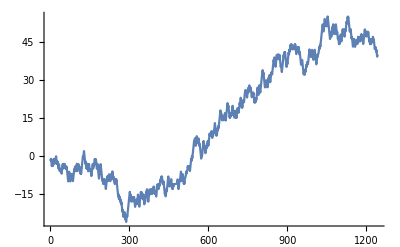

```mathematica
Plot[dsw[t],{t,dsw["FirstTime"],dsw["LastTime"]},PlotRange->All]
```

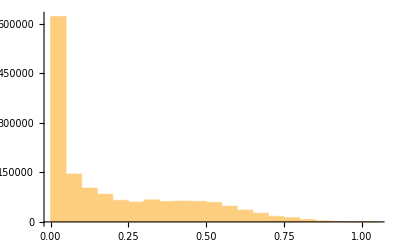

```mathematica
Histogram[Rescale[Flatten[dm]]]
```

```mathematica
Mean[Differences[ds["Times"]]]
```

1

CorrelationFunctionpaclet:ref/CorrelationFunction[data,hspec] estimates the correlation function at lags hspec from data.
hspec        | {τ_min,τ_max} | unit spaced from τ_min to τ_max

```mathematica
f=CorrelationFunction[ds,{1,1242}]
```

TimeSeries[…]

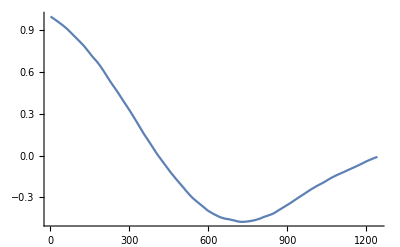

```mathematica
Plot[f[t],{t,1,1242},PlotRange->All]
```

```mathematica
FindRoot[f[t],{t,1}]
```

{t→409.373}

```mathematica
Fourier[data];
```

```mathematica
MinMax[Abs[Fourier[data]]]
```

{0.0572021,564.871}

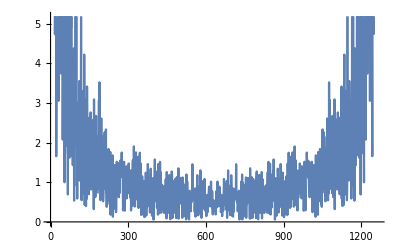

```mathematica
ListLinePlot[Abs[Fourier[data]],PlotRange->Automatic]
```

This is equivalent to the original estimate of the lag!

```mathematica
embedLag=RQAEstimateLag[ds]
```

409.373

```mathematica
RQAEstimateDimensionality[ds,embedLag]
```

First::nofirst: {} has zero length and no first element.

General::stop: Further output of First::nofirst will be suppressed during this calculation.

Part::pkspec1: The expression {First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»} cannot be used as a part specification.

MapThread::mptd: Object {-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,«13»,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

10 Mean[MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-4.,-3.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-7.,-8.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-5.,-6.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-5.,-6.,-5.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,-1.,0.,1.,2.,1.,0.,-1.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-11.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-10.,-11.,-12.,-13.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-18.,-19.,-18.,-19.,-20.,-21.,-22.,-21.,-22.,-23.,-24.,-23.,-22.,-23.,-22.,-23.,-24.,-25.,-24.,-25.,-26.,-25.,-24.,-23.,-24.,-23.,-22.,-21.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-19.,-18.,-17.,-18.,-19.,-18.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-18.,-17.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-13.,-14.,-15.,-16.,-17.,-18.,-17.,-16.,-15.,-14.,-13.,-14.,-15.,-14.,-15.,-14.,-13.,-14.,-13.,-14.,-15.,-14.,-13.,-14.,-13.,-12.,-13.,-12.,-13.,-14.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-11.,-12.,-13.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-10.,-11.,-12.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-10.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-9.,-8.,-7.,-8.,-7.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-2.,-1.,-2.,-1.,0.,-1.,0.,1.,2.,3.,4.,5.,6.,5.,6.,7.,6.,5.,4.,5.,6.,7.,8.,7.,6.,7.,6.,5.,6.,7.,6.,5.,4.,5.,4.,3.,2.,1.,0.,-1.,0.,1.,0.,1.,2.,3.,4.,5.,6.,5.,4.,3.,4.,3.,2.,1.,2.,3.,4.,3.,4.,5.,4.,5.,6.,5.,4.,5.,6.,7.,8.,9.,8.,7.,8.,9.,8.,9.,10.,9.,8.,7.,8.,9.,8.,9.,10.,9.,10.,11.,12.,13.,12.,11.,10.,9.,8.,9.,8.,9.,10.,11.,10.,11.,12.,11.,12.,13.,14.,15.,16.,17.,18.,17.,16.,17.,16.,15.,14.,15.,14.,15.,16.,15.,14.,15.,16.,15.,16.,17.,16.,15.,14.,15.,16.,17.,18.,19.,20.,21.,20.,19.,20.,19.,18.,17.,16.,15.,16.,15.,16.,17.,16.,17.,16.,17.,18.,19.,20.,19.,18.,17.,16.,17.,16.,15.,16.,17.,18.,17.,16.,15.,16.,15.,16.,17.,18.,19.,18.,19.,18.,17.,18.,19.,20.,21.,20.,21.,22.,23.,22.,21.,20.,19.,20.,19.,20.,21.,22.,21.,22.,21.,22.,23.,24.,25.,26.,25.,26.,25.,24.,25.,24.,23.,24.,25.,26.,27.,26.,25.,26.,27.,28.,27.,26.,27.,26.,27.,26.,25.,24.,23.,24.,25.,24.,25.,24.,25.,24.,23.,22.,21.,22.,21.,22.,21.,22.,23.,22.,23.,24.,25.,26.,27.,26.,25.,24.,25.,26.,27.,28.,27.,26.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,33.,32.,33.,32.,31.,30.,29.,28.,27.,28.,29.,28.,29.,30.,29.,28.,27.,28.,27.,28.,29.,30.,31.,30.,31.,32.,31.,30.,29.,30.,31.,32.,33.,32.,33.,32.,33.,34.,35.,36.,37.,38.,37.,38.,39.,38.,37.,36.,35.,36.,37.,38.,39.,40.,39.,38.,39.,40.,39.,40.,39.,38.,39.,40.,39.,38.,37.,36.,35.,36.,35.,34.,33.,34.,35.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,40.,39.,38.,37.,36.,35.,36.,37.,36.,37.,38.,39.,40.,41.,40.,41.,42.,41.,42.,43.,44.,43.,44.,43.,44.,43.,42.,43.,42.,43.,42.,43.,42.,43.,42.,43.,44.,43.,44.,43.,42.,41.,40.,41.,42.,41.,42.,43.,42.,43.,42.,43.,42.,41.,40.,41.,40.,39.,38.,37.,36.,37.,36.,37.,38.,37.,36.,35.,34.,33.,32.,33.,34.,33.,32.,33.,34.,33.,34.,35.,36.,35.,36.,37.,36.,37.,36.,37.,38.,39.,40.,41.,42.,41.,40.,41.,40.,39.,40.,39.,40.,41.,42.,41.,40.,39.,38.,39.,38.,39.,40.,41.,42.,41.,40.,39.,38.,37.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,42.,43.,42.,43.,44.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,51.,50.,49.,50.,51.,52.,53.,54.,53.,52.,51.,52.,51.,52.,51.,52.,53.,54.,55.,54.,53.,52.,51.,50.,49.,48.,47.,46.,47.,48.,49.,48.,47.,48.,49.,50.,51.,50.,51.,52.,51.,50.,49.,48.,49.,48.,49.,50.,51.,52.,51.,50.,49.,48.,49.,48.,47.,46.,47.,46.,45.,44.,45.,44.,45.,46.,47.,48.,47.,46.,45.,46.,47.,48.,49.,50.,49.,48.,49.,50.,49.,48.,47.,48.,49.,50.,49.,50.,51.,52.,53.,52.,53.,54.,55.,54.,55.,54.,53.,52.,51.,50.,49.,50.,49.,50.,49.,48.,47.,46.,47.,46.,45.,44.,43.,44.,45.,46.,45.,46.,45.,44.,43.,44.,45.,44.,45.,44.,45.,46.,45.,44.,45.,46.,47.,46.,47.,46.,45.,46.,47.,46.,45.,46.,47.,48.,47.,48.,47.,46.,47.,46.,45.,44.,45.,46.,47.,48.,49.,50.,49.,48.,49.,48.,47.,48.,49.,48.,49.,48.,47.,48.,49.,48.,47.,46.,45.,46.,45.,44.,45.,46.,45.,44.,45.,46.,45.,46.,45.,46.,47.,46.,45.,46.,45.,44.,43.,42.,43.,42.,43.,42.,41.,42.,41.,40.,39.,40.,39.,38.,37.,36.,37.,38.,37.,36.,35.,34.,35.,36.,37.,36.,35.,34.,35.,34.,33.,34.,33.},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-4.,-3.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-7.,-8.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-6.,-5.,-6.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-5.,-6.,-5.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-3.,-2.,-1.,0.,-1.,0.,1.,2.,1.,0.,-1.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,-3.,-4.,-3.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-8.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-6.,-7.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-11.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-8.,-9.,-10.,-9.,-10.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-10.,-11.,-12.,-13.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-18.,-19.,-18.,-19.,-20.,-21.,-22.,-21.,-22.,-23.,-24.,-23.,-22.,-23.,-22.,-23.,-24.,-25.,-24.,-25.,-26.,-25.,-24.,-23.,-24.,-23.,-22.,-21.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-17.,-16.,-17.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-19.,-18.,-17.,-18.,-19.,-18.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-20.,-19.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-16.,-17.,-16.,-15.,-16.,-17.,-18.,-19.,-18.,-17.,-18.,-17.,-16.,-15.,-14.,-15.,-14.,-13.,-14.,-15.,-16.,-17.,-18.,-17.,-16.,-15.,-14.,-13.,-14.,-15.,-14.,-15.,-14.,-13.,-14.,-13.,-14.,-15.,-14.,-13.,-14.,-13.,-12.,-13.,-12.,-13.,-14.,-15.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-9.,-10.,-9.,-8.,-9.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-11.,-12.,-13.,-14.,-15.,-14.,-15.,-16.,-15.,-14.,-13.,-14.,-13.,-12.,-11.,-10.,-9.,-8.,-9.,-10.,-11.,-12.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-12.,-11.,-12.,-13.,-12.,-13.,-12.,-11.,-10.,-11.,-12.,-11.,-12.,-11.,-10.,-9.,-10.,-11.,-12.,-13.,-12.,-11.,-10.,-9.,-10.,-9.,-8.,-7.,-6.,-7.,-8.,-9.,-10.,-9.,-8.,-7.,-8.,-9.,-10.,-11.,-10.,-11.,-10.,-9.,-8.,-7.,-8.,-7.,-6.,-7.,-6.,-7.,-6.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-4.,-5.,-6.,-5.,-4.,-3.,-2.,-1.,-2.,-1.,0.,-1.,0.,1.,2.,3.,4.,5.,6.,5.,6.,7.,6.,5.,4.,5.,6.,7.,8.,7.,6.,7.,6.,5.,6.,7.,6.,5.,4.,5.,4.,3.,2.,1.,0.,-1.,0.,1.,0.,1.,2.,3.,4.,5.,6.,5.,4.,3.,4.,3.,2.,1.,2.,3.,4.,3.,4.,5.,4.,5.,6.,5.,4.,5.,6.,7.,8.,9.,8.,7.,8.,9.,8.,9.,10.,9.,8.,7.,8.,9.,8.,9.,10.,9.,10.,11.,12.,13.,12.,11.,10.,9.,8.,9.,8.,9.,10.,11.,10.,11.,12.,11.,12.,13.,14.,15.,16.,17.,18.,17.,16.,17.,16.,15.,14.,15.,14.,15.,16.,15.,14.,15.,16.,15.,16.,17.,16.,15.,14.,15.,16.,17.,18.,19.,20.,21.,20.,19.,20.,19.,18.,17.,16.,15.,16.,15.,16.,17.,16.,17.,16.,17.,18.,19.,20.,19.,18.,17.,16.,17.,16.,15.,16.,17.,18.,17.,16.,15.,16.,15.,16.,17.,18.,19.,18.,19.,18.,17.,18.,19.,20.,21.,20.,21.,22.,23.,22.,21.,20.,19.,20.,19.,20.,21.,22.,21.,22.,21.,22.,23.,24.,25.,26.,25.,26.,25.,24.,25.,24.,23.,24.,25.,26.,27.,26.,25.,26.,27.,28.,27.,26.,27.,26.,27.,26.,25.,24.,23.,24.,25.,24.,25.,24.,25.,24.,23.,22.,21.,22.,21.,22.,21.,22.,23.,22.,23.,24.,25.,26.,27.,26.,25.,24.,25.,26.,27.,28.,27.,26.,25.,26.,27.,28.,29.,30.,31.,32.,33.,34.,33.,32.,33.,32.,31.,30.,29.,28.,27.,28.,29.,28.,29.,30.,29.,28.,27.,28.,27.,28.,29.,30.,31.,30.,31.,32.,31.,30.,29.,30.,31.,32.,33.,32.,33.,32.,33.,34.,35.,36.,37.,38.,37.,38.,39.,38.,37.,36.,35.,36.,37.,38.,39.,40.,39.,38.,39.,40.,39.,40.,39.,38.,39.,40.,39.,38.,37.,36.,35.,36.,35.,34.,33.,34.,35.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,40.,39.,38.,37.,36.,35.,36.,37.,36.,37.,38.,39.,40.,41.,40.,41.,42.,41.,42.,43.,44.,43.,44.,43.,44.,43.,42.,43.,42.,43.,42.,43.,42.,43.,42.,43.,44.,43.,44.,43.,42.,41.,40.,41.,42.,41.,42.,43.,42.,43.,42.,43.,42.,41.,40.,41.,40.,39.,38.,37.,36.,37.,36.,37.,38.,37.,36.,35.,34.,33.,32.,33.,34.,33.,32.,33.,34.,33.,34.,35.,36.,35.,36.,37.,36.,37.,36.,37.,38.,39.,40.,41.,42.,41.,40.,41.,40.,39.,40.,39.,40.,41.,42.,41.,40.,39.,38.,39.,38.,39.,40.,41.,42.,41.,40.,39.,38.,37.,36.,37.,38.,39.,40.,39.,40.,41.,40.,41.,42.,43.,42.,43.,44.,43.,44.,45.,46.,47.,48.,49.,50.,51.,52.,51.,50.,49.,50.,51.,52.,53.,54.,53.,52.,51.,52.,51.,52.,51.,52.,53.,54.,55.,54.,53.,52.,51.,50.,49.,48.,47.,46.,47.,48.,49.,48.,47.,48.,49.,50.,51.,50.,51.,52.,51.,50.,49.,48.,49.,48.,49.,50.,51.,52.,51.,50.,49.,48.,49.,48.,47.,46.,47.,46.,45.,44.,45.,44.,45.,46.,47.,48.,47.,46.,45.,46.,47.,48.,49.,50.,49.,48.,49.,50.,49.,48.,47.,48.,49.,50.,49.,50.,51.,52.,53.,52.,53.,54.,55.,54.,55.,54.,53.,52.,51.,50.,49.,50.,49.,50.,49.,48.,47.,46.,47.,46.,45.,44.,43.,44.,45.,46.,45.,46.,45.,44.,43.,44.,45.,44.,45.,44.,45.,46.,45.,44.,45.,46.,47.,46.,47.,46.,45.,46.,47.,46.,45.,46.,47.,48.,47.,48.,47.,46.,47.,46.,45.,44.,45.,46.,47.,48.,49.,50.,49.,48.,49.,48.,47.,48.,49.,48.,49.,48.,47.,48.,49.,48.,47.,46.,45.,46.,45.,44.,45.,46.,45.,44.,45.,46.,45.,46.,45.,46.,47.,46.,45.,46.,45.,44.,43.,42.,43.,42.,43.,42.,41.,42.,41.,40.,39.,40.,39.,38.,37.,36.,37.,38.,37.,36.,35.,34.,35.,36.,37.,36.,35.,34.,35.,34.,33.,34.,33.}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,5,6,5,6,5,6,31,6,31,6,31,6,31,36,43,First[{}],First[{}],First[{}],67,66,43,36,43,66,67,68,67,66,43,66,43,66,43,66,67,68,67,66,43,36,31,36,31,6,31,6,31,36,31,6,5,6,31,36,31,6,5,6,31,6,31,36,31,36,43,36,43,36,31,6,5,2,1,22,1,22,First[{}],First[{}],127,22,1,2,5,2,5,6,31,6,31,6,5,6,31,36,31,6,5,6,31,36,31,36,31,36,43,66,43,36,31,6,5,6,31,6,5,6,5,2,1,2,5,2,1,2,5,6,31,6,5,6,31,36,43,66,67,66,43,36,31,6,5,6,31,36,43,66,67,68,67,68,First[{}],68,67,68,67,68,201,68,201,First[{}],First[{}],210,201,68,67,66,67,66,67,68,67,66,43,66,67,66,67,68,67,66,43,66,67,66,43,36,43,66,67,66,67,68,67,68,201,68,67,68,67,68,67,68,201,210,211,First[{}],First[{}],First[{}],257,258,First[{}],258,261,258,261,First[{}],261,266,First[{}],266,269,269,272,First[{}],273,274,First[{}],First[{}],277,274,277,274,277,278,278,278,285,285,285,278,277,278,277,274,273,272,269,266,261,258,257,256,257,258,257,258,261,266,261,258,261,258,261,266,261,258,261,258,261,266,269,272,269,266,269,266,261,266,269,266,261,258,257,258,261,266,269,272,269,266,261,258,257,256,257,256,257,258,257,258,261,258,257,258,261,266,269,266,261,266,261,258,257,256,257,256,211,256,257,258,261,266,261,258,257,256,211,256,257,256,257,256,211,256,211,256,257,256,211,256,211,210,211,210,211,256,257,256,257,256,257,258,257,256,211,210,201,210,211,210,211,210,201,210,201,68,67,68,67,68,67,66,67,66,67,68,201,68,201,68,201,210,211,256,257,256,257,258,257,256,211,256,211,210,201,68,67,66,67,68,201,210,201,210,201,210,201,68,67,68,201,210,211,210,211,210,201,210,201,210,211,210,211,210,201,68,201,210,201,210,201,68,67,68,201,210,211,210,201,68,67,68,67,66,43,36,43,66,67,68,67,66,43,66,67,68,201,68,201,68,67,66,43,66,43,36,43,36,43,36,31,6,31,6,31,6,31,6,31,36,31,6,5,2,1,2,1,22,1,22,127,128,First[{}],First[{}],First[{}],First[{}],545,546,First[{}],546,545,544,545,546,549,First[{}],549,546,549,546,545,546,549,546,545,544,545,544,543,128,127,22,1,22,127,22,127,128,543,544,545,546,545,544,543,544,543,128,127,128,543,544,543,544,545,544,545,546,545,544,545,546,549,556,First[{}],556,549,556,605,556,605,First[{}],605,556,549,556,605,556,605,612,605,612,First[{}],623,624,624,623,612,605,556,605,556,605,612,623,612,623,624,623,624,625,First[{}],First[{}],First[{}],First[{}],First[{}],645,644,645,644,643,642,643,642,643,644,643,642,643,644,643,644,645,644,643,642,643,644,645,646,First[{}],First[{}],First[{}],672,671,672,671,646,645,644,643,644,643,644,645,644,645,644,645,646,671,672,671,646,645,644,645,644,643,644,645,646,645,644,643,644,643,644,645,646,671,646,671,646,645,646,671,672,673,672,673,First[{}],First[{}],722,673,672,671,672,671,672,673,722,673,722,673,722,723,First[{}],First[{}],First[{}],739,740,739,738,739,738,723,738,739,740,First[{}],740,739,740,751,First[{}],751,740,751,740,751,740,739,738,723,738,739,738,739,738,739,738,723,722,673,722,673,722,673,722,723,722,723,738,739,740,751,740,739,738,739,740,751,756,751,740,739,740,751,756,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],805,804,805,804,803,802,801,756,751,756,801,756,801,802,801,756,751,756,751,756,801,802,803,802,803,804,803,802,801,802,803,804,805,804,805,804,805,806,First[{}],First[{}],First[{}],First[{}],847,848,First[{}],848,847,846,845,846,847,848,851,First[{}],851,848,851,860,851,860,851,848,851,860,851,848,847,846,845,846,845,806,805,806,845,846,847,848,851,860,851,860,First[{}],860,889,860,851,848,847,846,845,846,847,846,847,848,851,860,889,860,889,First[{}],889,908,First[{}],First[{}],911,912,911,912,911,908,911,908,911,908,911,908,911,908,911,912,911,912,911,908,889,860,889,908,889,908,911,908,911,908,911,908,889,860,889,860,851,848,847,846,847,846,847,848,847,846,845,806,805,804,805,806,805,804,805,806,805,806,845,846,845,846,847,846,847,846,847,848,851,860,889,908,889,860,889,860,851,860,851,860,889,908,889,860,851,848,851,848,851,860,889,908,889,860,851,848,847,846,847,848,851,860,851,860,889,860,889,908,911,908,911,912,911,912,First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],First[{}],1033,1032,1031,1032,1033,1034,First[{}],First[{}],1041,1034,1033,1034,1033,1034,1033,1034,1041,1042,1042,1042,1041,1034,1033,1032,1031,1030,1029,1028,1029,1030,1031,1030,1029,1030,1031,1032,1033,1032,1033,1034,1033,1032,1031,1030,1031,1030,1031,1032,1033,1034,1033,1032,1031,1030,1031,1030,1029,1028,1029,1028,1027,912,1027,912,1027,1028,1029,1030,1029,1028,1027,1028,1029,1030,1031,1032,1031,1030,1031,1032,1031,1030,1029,1030,1031,1032,1031,1032,1033,1034,1041,1034,1041,1042,1053,1042,1053,1042,1041,1034,1033,1032,1031,1032,1031,1032,1031,1030,1029,1028,1029,1028,1027,912,911,912,1027,1028,1027,1028,1027,912,911,912,1027,912,1027,912,1027,1028,1027,912,1027,1028,1029,1028,1029,1028,1027,1028,1029,1028,1027,1028,1029,1030,1029,1030,1029,1028,1029,1028,1027,912,1027,1028,1029,1030,1031,1032,1031,1030,1031,1030,1029,1030,1031,1030,1031,1030,1029,1030,1031,1030,1029,1028,1027,1028,1027,912,1027,1028,1027,912,1027,1028,1027,1028,1027,1028,1029,1028,1027,1028,1027,912,911,908,911,908,911,908,889,908,889,860,851,860,851,848,847,846,847,848,847,846,845,806,845,846,847,846,845,806,845,806,805,806,805}⟧}]]

Part::pkspec1: The expression {3,24,1,18,53,46,17,12,7,102,7,8,12,12,13,8,7,4,18,18,19,3,1,2,33,28,25,26,28,25,32,34,25,32,61,42,41,40,93,38,37,36,42,42,35,6,5,6,37,10,«803»} cannot be used as a part specification.

MapThread::mptd: Object {{-1.,-12.3732},{-2.,-12.6268},{-1.,-11.6268},{-2.,-11.3732},{-3.,-11.6268},{-4.,-10.6268},{-3.,-9.62677},{-2.,-9.37323},{-3.,-9.62677},«33»,{-7.,-11.6268},{-6.,-11.3732},{-5.,-11.6268},{-4.,-11.3732},{-3.,-11.6268},{-4.,-10.6268},{-5.,-9.62677},{-4.,-9.37323},«803»}⟦{3,24,1,«46»,10,«803»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{{-1.,-12.3732},{-2.,-12.6268},{-1.,-11.6268},{-2.,-11.3732},{-3.,-11.6268},{-4.,-10.6268},{-3.,-9.62677},{-2.,-9.37323},{-3.,-9.62677},«34»,{-6.,-11.3732},{-5.,-11.6268},{-4.,-11.3732},{-3.,-11.6268},{-4.,-10.6268},{-5.,-9.62677},{-4.,-9.37323},«803»},{«1»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

MapThread::mptd: Object {-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{First[{}],First[{}],1,2,First[{}],First[{}],5,2,5,6,5,2,1,2,1,2,5,2,1,2,1,First[{}],1,2,5,2,5,2,5,6,First[{}],6,5,6,31,First[{}],31,36,31,36,31,36,First[{}],36,31,6,5,6,31,6,«1213»}⟧ at position {2, 2} in MapThread[SquaredEuclideanDistance,{{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,-2.,-1.,0.,-1.,-2.,-3.,-2.,-3.,-2.,-3.,-4.,-5.,-4.,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»},{-1.,-2.,-1.,-2.,-3.,-4.,-3.,-2.,-3.,-4.,-3.,-2.,-1.,-2.,-1.,-2.,-3.,-2.,-1.,«13»,-3.,-4.,-5.,-6.,-5.,-6.,-5.,-6.,-5.,-6.,-7.,-6.,-5.,-4.,-3.,-4.,-5.,-4.,«1213»}⟦{«1»}⟧}] has only 0 of required 1 dimensions.

General::stop: Further output of MapThread::mptd will be suppressed during this calculation.

{Null,{{{2,0.,2,Mean[1],2,Mean[MapThread[SquaredEuclideanDistance,{{{-1.,-12.3732},{-2.,-12.6268},{-1.,-11.6268},{-2.,-11.3732},{-3.,-11.6268},{-4.,-10.6268},{-3.,-9.62677},839,{37.,35.6268},{38.,34.6268},{37.,34.3732},{38.,34.6268},{39.,33.6268},{38.,33.3732},{37.,33.6268}},1}]]}}}}
 |  |  |  |

## Time Series Epochs start here

RQATimeSeriesEpochs[ts_,wid_,overlap_]:=
Table[TimeSeriesWindow[ts,{t0,t0+wid}],{t0,ts[“FirstTime”],ts[“LastTime”]-wid,overlap}]

```mathematica
e=RQATimeSeriesEpochs[dsw,200,50];
```

```mathematica
Head[%];
```

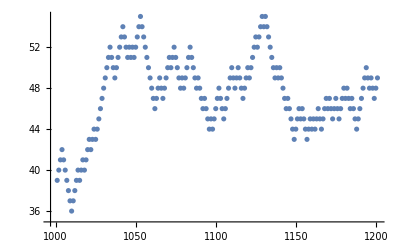

```mathematica
ListPlot[e[[-1]]]
```

If TimeSeriesEpochs defines the windows, how do you talk to the windows, compute the RQA, plot them?
6July2019 Getting there

So for each part of list e, calculate the following, with ds replaced by that part of the list:

```mathematica
embedding=RQAEmbed[e[[-1]],3,lag]
```

TimeSeries[…]

```mathematica
rm=RQARecurrenceMap[embedding];
```

```mathematica
RQARecurrence[rm]//N
```

0.62302

```mathematica
RQADeterminism[rm]//N
```

0.979505

```mathematica
RQALaminarity[rm,3]//N
```

0.972313

```mathematica
RQATrappingTime[rm]//N
```

15.1545

```mathematica
RQATrend[rm]//N
```

-153.394

```mathematica
RQAEntropy[rm]//N
```

4.39655

```mathematica
RQAChaos[rm]//N
```

0.00555556

```mathematica
RQADmax[rm,2]//N
```

180.

```mathematica
RQAVmax[rm,2]//N
```

83.

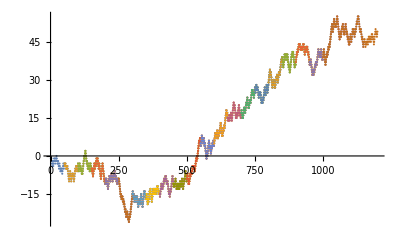
Map[-Graphics-]

```mathematica
Map[ListPlot[e]]
```

```mathematica
len=Length[e]
```

21

```mathematica
e[[3]]//N
```

TimeSeries[…]

```mathematica
Do[ListPlot[e[[i]]],{i,len}]
```

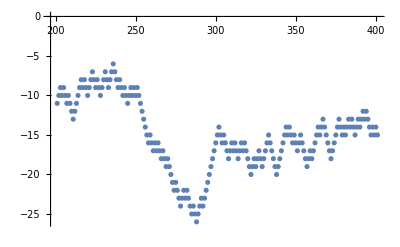

```mathematica
ListPlot[e[[5]]]
```

for each part of list e you need to calculate:
1. RQAEmbed[e[[part]],3,lag]
2. RQARecurrenceMap[RQAEmbed[e[[part]],3,lag]]
3. all the RQAs

copied from Flip Phillips epochs for alison.nb

```mathematica
eps=RQATimeSeriesEpochs[dsw,200,50];
```

So the following estimates the lag for each of the time series, eps 
Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
Head[eps]
```

List

```mathematica
taus=Map[RQAEstimateLag,eps]
```

InterpolatingFunction::dmval: Input value {1} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {2} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {3} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

{20.9696,40.9543,65.0895,71.1767,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709,73.5709}

```mathematica
Mean[%]
```

68.995

RQAEmbed::usage=”RQAEmbed[ts,dims,tau] but why.”
#   Slot   represents the first argument supplied to a pure function. 
embeds as follows gives a list of TimeSeries, each of which it should be possible to address and plot separately.

```mathematica
embeds=Map[RQAEmbed[#,3,30.0]&,eps];
```

```mathematica
embeds=Map[RQAEmbed[#,3,10.0]&,eps];
```

```mathematica
Head[embeds]
```

List

N doesnt, and won’t, work here as it gives the numerical value of an expression, it does not count things.

```mathematica
N[embeds];
```

These bits of code successfully plot coloured squares for each epoch for the distance map

Mappaclet:ref/Map[f,expr] or f/@expr   applies f to each element on the first level in expr.

```mathematica
maps=RQADistanceMap/@embeds;
```

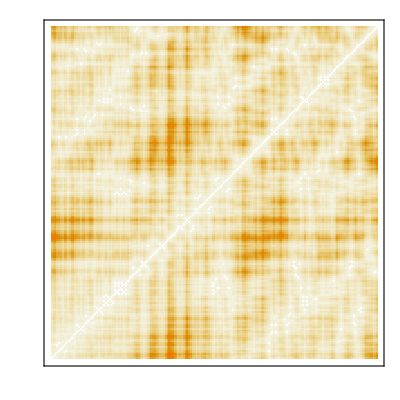
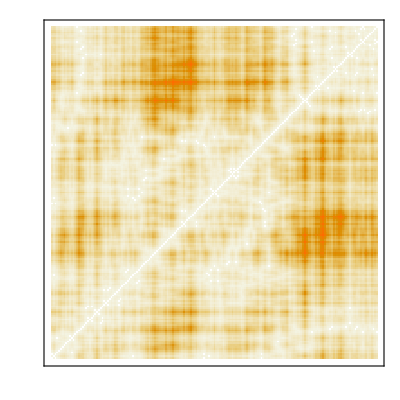
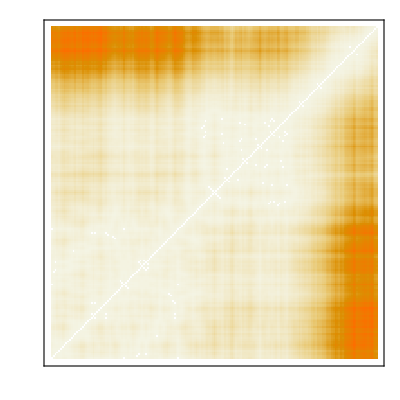
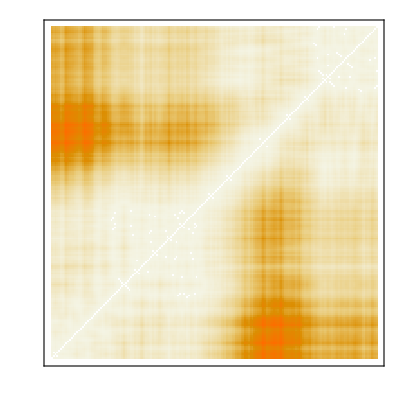
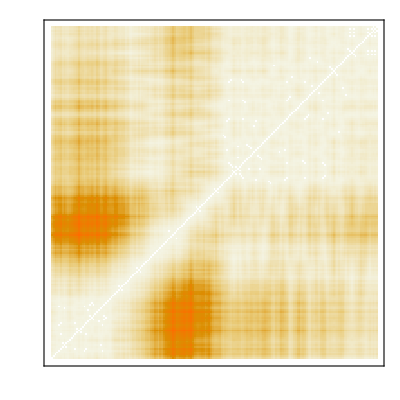
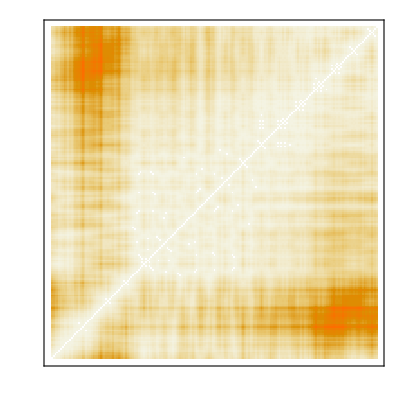
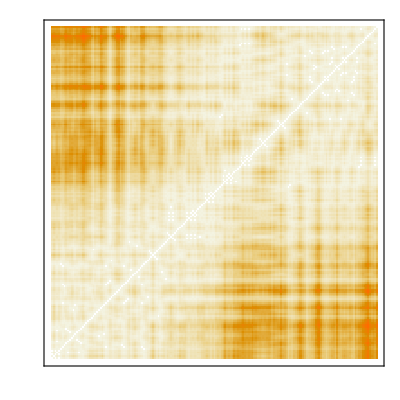
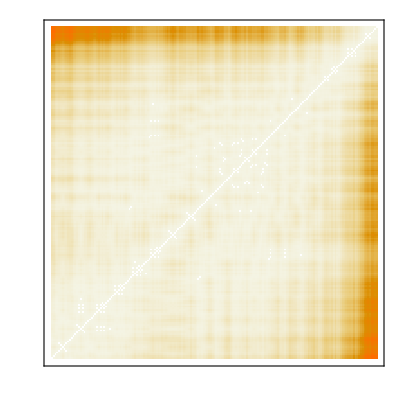

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None]&/@maps
```

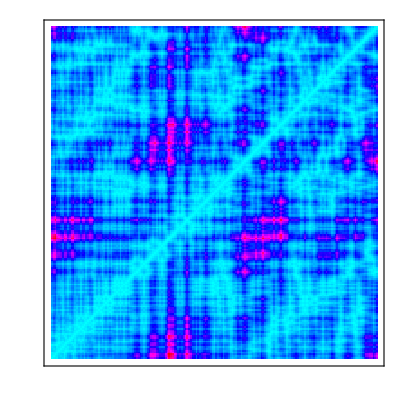
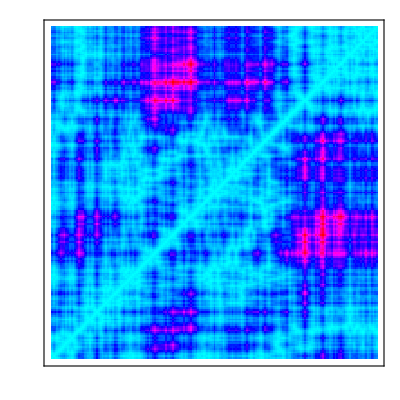
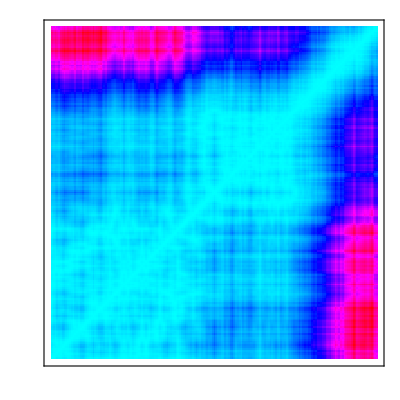
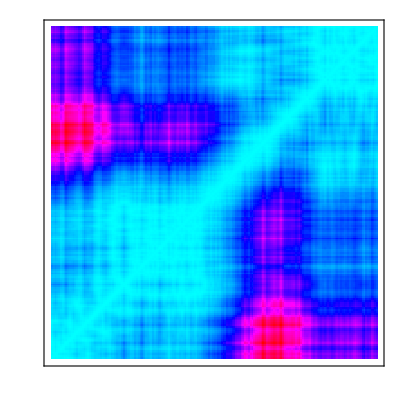
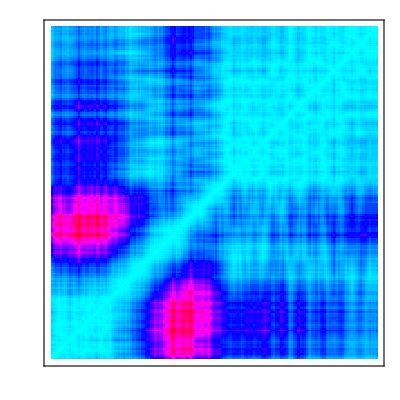
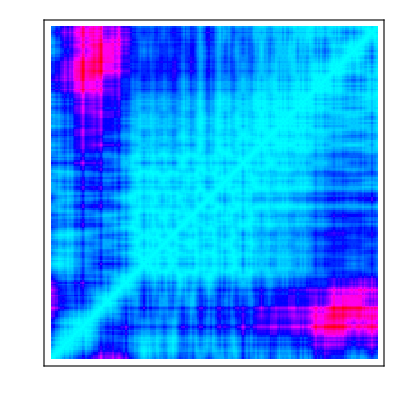
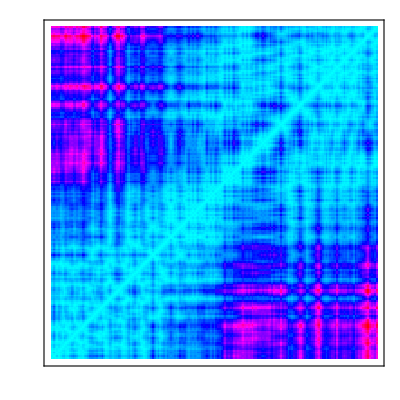
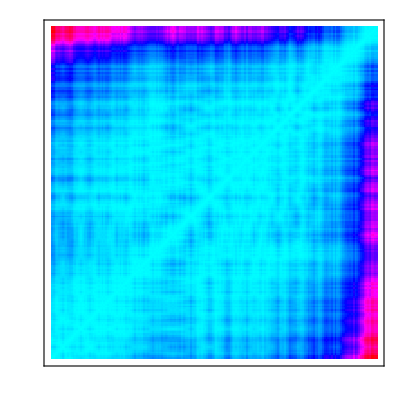
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@maps
```

```mathematica
(* numbers=RQARecurrenceMap[#,.01]&/@embeds; *)
```

```mathematica
numbers=RQARecurrenceMap[#]&/@embeds;
```

and for the recurrence map

```mathematica
MatrixPlot[#,DataReversed->{True,False},FrameTicks->None,ColorFunction->Hue]&/@numbers
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

I am still stuck with trying to obtain the RQA measures for each plot for each epoch - solved by Flip!  apply RQADeterminism etc. to numbers not to embeds

```mathematica
N[RQADeterminism/@numbers]
```

{0.962624,0.97626,0.995963,0.989643,0.986697,0.979634,0.982475,0.994199,0.996031,0.993156,0.992213,0.994257,0.985229,0.985433,0.993531,0.992845,0.986974,0.991929,0.990031,0.992876,0.979505}

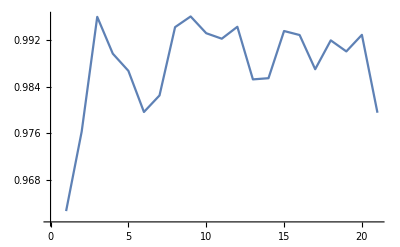

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQALaminarity/@numbers]
```

{0.952095,0.983895,0.99842,0.991988,0.989925,0.986552,0.980211,0.995276,0.994098,0.993558,0.992886,0.994736,0.98465,0.985717,0.994673,0.994392,0.988484,0.992455,0.989249,0.990569,0.985516}

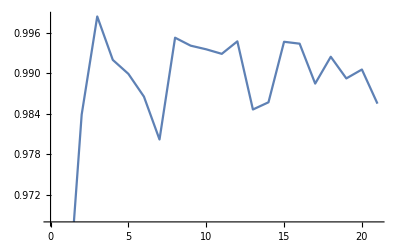

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQATrappingTime/@numbers]
```

{9.92645,10.7643,43.7538,29.429,23.211,19.2838,18.1679,37.6458,46.9663,40.9585,41.312,47.6743,28.6489,28.0889,33.729,34.6296,26.5114,25.8288,31.0491,33.8116,15.1545}

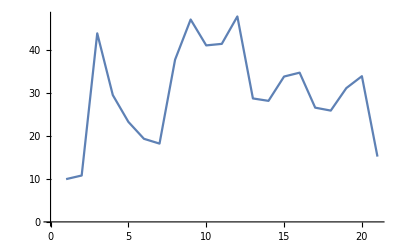

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQATrend/@numbers]
```

General::munfl: Exp[-794.283] is too small to represent as a normalized machine number; precision may be lost.

{-132.39,-204.223,-192.545,-247.19,-219.291,-226.529,-248.943,-159.557,-274.799,-282.868,-262.122,-265.027,-263.015,-254.595,-259.718,-271.75,-194.256,-124.57,-251.523,-248.238,-153.394}

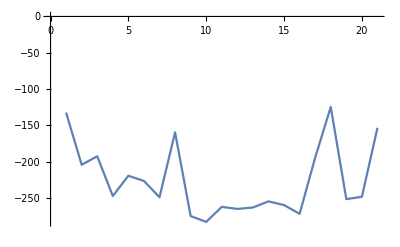

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQAEntropy/@numbers]
```

{3.81772,4.09465,5.82215,5.15516,4.79727,4.29505,4.52057,5.09415,6.04073,5.64591,5.25132,5.35709,4.53207,4.84165,5.19177,5.48023,5.14052,5.14919,5.15182,5.00428,4.39655}

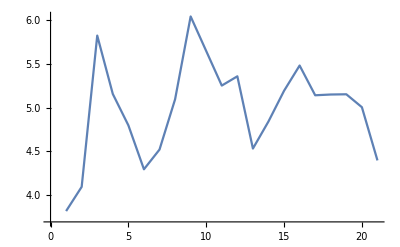

```mathematica
ListLinePlot[%]
```

```mathematica
N[RQAChaos/@numbers]
```

{0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556,0.00555556}

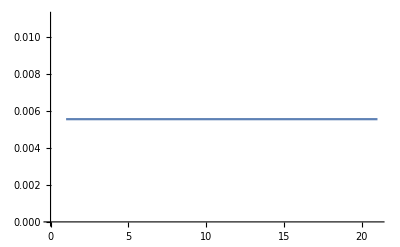

```mathematica
ListLinePlot[%]
```

DMax and VMax require a threshold - how do you write this?

```mathematica
N[RQADMax[#,2]/@numbers]
```

{RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],7,RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}],RQADMax[#1,2.][{1}]}
 |  |  |  |

```mathematica
ListLinePlot[%]
```

-Graphics-

```mathematica
N[RQAVMax/@numbers]
```

{RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}],RQAVMax[{1}]}
 |  |  |  |

```mathematica
ListLinePlot[%]
```

-Graphics-